# Control the Center: An empirical study of the effect of controlling the center on outcomes in chess

## Willem Nielsen

## Goal

My goal is to determine if we can find empirically in chess data that there is an advantage to controlling the center. We take games from Lichess of various ratings. We identify the last two turns where the game was materially balanced. This is because we want to see if there is an advantage to controlling the center without a material advantage. We then take the attacked squares at those last two turns. We compare the frequency of attacking each square between the winners and the losers. If the winners attack the middle squares more frequently, then we reject the null hypothesis that there is no advantage to controlling the center.

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
ResourceFunction["DarkMode"][False]
PacletInstall["Wolfram/Chess"]
Needs["Wolfram`Chess`"]
```

/Users/erichegonzales/Projects/Wolfram/SummerSchool

PacletObject[…]

### Importing and Processing

Import first in FENS so you can identify malformed games. The import time for the Chess Paclet is slow, I’ve found that importing 50 games takes about 30 seconds. This needs to be sped up so we can get enough data.

```mathematica
fensImport=Import["/Users/erichegonzales/Projects/Wolfram/SummerSchool/lichess_db_standard_rated_2013-01.pgn",{"FENStrings", 201;;1000}];
```

Import::fmterr: Cannot import data as PGN format.

General::stop: Further output of Import::fmterr will be suppressed during this calculation.

Then import games in the ChessGames Paclet Object format

```mathematica
games=Import["/Users/erichegonzales/Projects/Wolfram/SummerSchool/lichess_db_standard_rated_2013-01.pgn",{"ChessGames", 201;;1000}];
```

Find positions of the failed imports and drop them

```mathematica
posFailed = Position[fensImport, $Failed]
```

{{2},{6},{8},{11},{26},{51},{76},{98},{112},{114},{134},{137},{157},{187},{232},{236},{240},{254},{267},{293},{298},{315},{355},{376},{381},{399},{400},{402},{404},{430},{446},{489},{495},{507},{510},{511},{522},{532},{540},{541},{543},{563},{575},{583},{588},{589},{594},{597},{604},{616},{625},{629},{660},{684},{687},{690},{719},{720},{725},{747},{763},{778},{779},{781},{783}}

```mathematica
games2 = Delete[games, posFailed];
fens = Delete[fensImport, posFailed];
winners = 
If[#["Result"]=="1-0", "White",
If[#["Result"]=="0-1", "Black", "Draw"]]&/@ games2;
```

```mathematica
boards  = Map[Chessboard, fens, {2}];
```

### Functions

```mathematica
getLastBalancedIdx[matBalance_]:=ResourceFunction["SelectPositions"][Reverse[matBalance], Abs[#]<=3&, 1][[1, 1]]*-1
getij[square_]:={Interpreter["Number"][StringPart[square, 2]], LetterNumber[StringPart[square, 1]]}
sortBoardPair[boardPair_, winner_]:= 
If[boardPair[[1]]["ActivePlayer"] == winner, {boardPair[[1]], boardPair[[2]]}, {boardPair[[2]], boardPair[[1]]}];
getAttackArray[attackedSquares_]:=
ReplacePart[ConstantArray[0, {8, 8}], (getij/@ attackedSquares)->1]
```

### Analysis

First we get the “last balanced boards” which is the last two turns of the game where the material is balanced (within 3 points)

```mathematica
matBalances = Map[#["MaterialBalance"]&, boards, {2}];
lbIdxs = {#-1,#}&/@(getLastBalancedIdx /@ matBalances);
lbBoards = MapThread[#1[[#2]] &,{boards, lbIdxs}] ;
```

We sort the boardPairs so that the winner is always the first board, so we can identify the winner easily

```mathematica
lbBoardsSorted = MapThread[sortBoardPair[#1, #2]&, {lbBoards, winners}];
```

Next we find the attacked squares of those two boards

```mathematica
attackedSquares = Map[{#[[1]]["AttackedSquares"],#[[2]]["AttackedSquares"]}&, lbBoards];
attackedSquaresList = Map[#["AttackedSquares"]&, lbBoardsSorted, {2}];
attackArrays = Map[getAttackArray, attackedSquaresList, {2}];
winnerAttackArrays = attackArrays[[All, 1]];
loserAttackArrays = attackArrays[[All, 2]];
```

### Visualization

Total attack squares for winners and losers

```mathematica
Total[winnerAttackArrays, 3]
Total[loserAttackArrays, 3]
```

24014

22224

```mathematica
Reverse[Total[winnerAttackArrays]][[8, 8]]
```

289

```mathematica
TableForm[{{Style["Winners", Large], Style["Losers", Large]},
{Grid[Reverse[Total[winnerAttackArrays]]], Grid[Reverse[Total[loserAttackArrays]]]}}]
```

Winners | Losers
225 | 329 | 338 | 347 | 359 | 366 | 341 | 276
270 | 236 | 300 | 364 | 342 | 426 | 371 | 372
337 | 338 | 387 | 408 | 443 | 452 | 440 | 407
261 | 407 | 424 | 478 | 472 | 475 | 432 | 314
299 | 385 | 401 | 489 | 474 | 454 | 423 | 330
406 | 403 | 438 | 419 | 460 | 442 | 443 | 405
297 | 269 | 315 | 389 | 383 | 412 | 347 | 389
234 | 373 | 373 | 387 | 381 | 391 | 377 | 289 | 203 | 361 | 362 | 367 | 358 | 371 | 347 | 241
300 | 254 | 286 | 375 | 354 | 384 | 347 | 352
378 | 405 | 405 | 421 | 422 | 424 | 414 | 377
284 | 371 | 420 | 434 | 459 | 440 | 412 | 276
266 | 393 | 394 | 447 | 435 | 395 | 407 | 282
352 | 345 | 364 | 360 | 382 | 380 | 393 | 353
265 | 227 | 272 | 320 | 300 | 372 | 319 | 317
208 | 299 | 301 | 301 | 311 | 326 | 303 | 231

Density of attack squares for winners

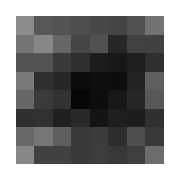
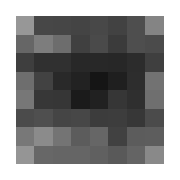
Winners | Losers
-Graphics- | -Graphics-

```mathematica
TableForm[{{Style["Winners", Large], Style["Losers", Large]},
{ArrayPlot[Reverse[Total[winnerAttackArrays]], PlotRange->{0,500}, ImageSize->Small], ArrayPlot[Reverse[Total[loserAttackArrays]], PlotRange->{0, 500}, ImageSize->Small]}}]
```

```mathematica
TableForm[{{Style["Winners", Large], Style["Losers", Large]},
{ListDensityPlot[Total[winnerAttackArrays], Mesh->None, InterpolationOrder->1],ListDensityPlot[Total[loserAttackArrays], Mesh->None, InterpolationOrder->1]} }]
```

Winners | Losers
-Graphics- | -Graphics-

```mathematica
attackPlots = Map[ArrayPlot[#, ImageSize->Tiny]&, attackArrays, {2}];
```

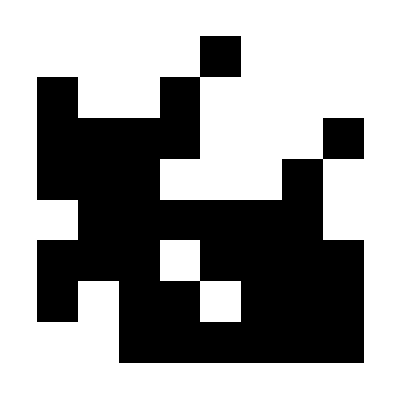
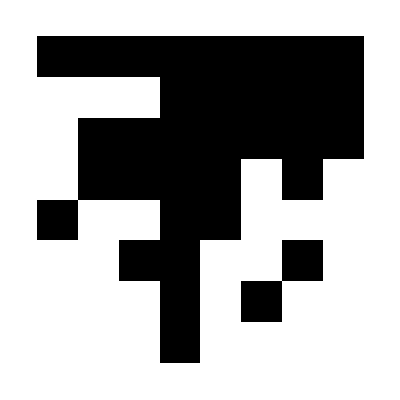
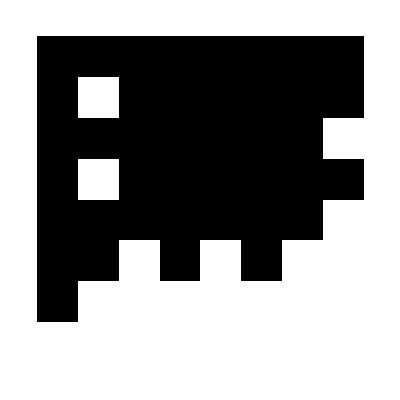
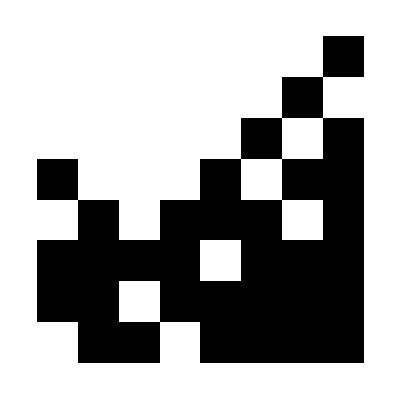
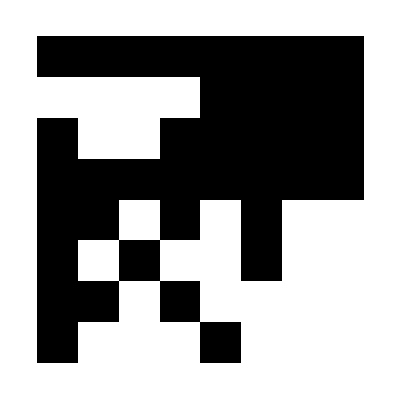
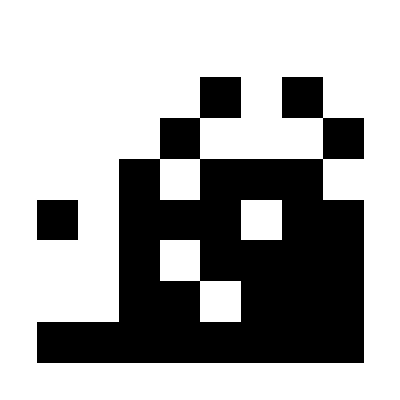
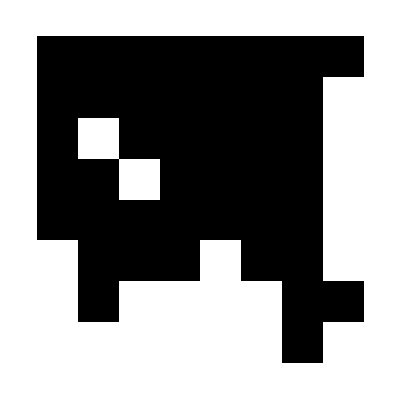
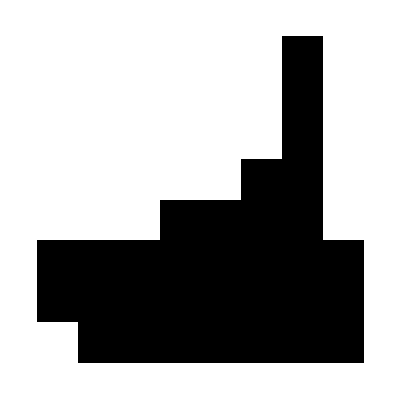
Winners | Losers
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
TableForm[Prepend[attackPlots[[;;5]], {"Winners", "Losers"}]]
```